# Sudakov Double Logs for Muon Collider

## Initialization and definitions

#### FeynArts Initialization

Loading FeynArts, FeynCalc and VecSet

```mathematica
FeynArtsDirectory="C:\\Users\\alfre\\Documents\\FeynArts\\";
Get[FeynArtsDirectory<>"/FeynArts-3.11/FeynArts.m"];
Get[FeynArtsDirectory<>"/FormCalc-9.9/FormCalc.m"];
Get[FeynArtsDirectory<>"/FormCalc-9.9/tools/VecSet.m"];
$FAVerbose=False;
$FCVerbose=False;
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

#### Numerical Parameters

Standard Model Parameters

```mathematica
(* Masses *)
mh=125.00000;
mz=91.18760;
mw=79.82240;
mt=172.76;

(* Couplings *)
Gf=1.166370 10^-5;
cosw=mw/mz;
sinw=(1-cosw^2)^(1/2);
α=(Gf √2 mw^2(1-mw^2/mz^2)/π);
el=√(4π α);
g=el/sinw;
g1=el/cosw;
v=2 mw/g;

Table[CKMnum[i,j]={
{0.9743289966291863,0.22509845918522653,0.0015484608354714617-0.0033603971552498115 ⅈ},
{-0.22496529664843487-0.000137285310773075 ⅈ,0.9734641722320304-0.000031716917007187496 ⅈ,0.0419297129881677},
{0.007931049223717068-0.003271275347509935 ⅈ,-0.0412021464690793-0.0007557601619603127 ⅈ,0.9991137118310057}
}[[i,j]],{i,1,3},{j,1,3}];


noCKM={CKM[x_,y_]:>KroneckerDelta[x,y],CKMC[x_,y_]:>KroneckerDelta[x,y],a->1,b->1};

toNumbers={gg->g,gg1->g1,CW->cosw,SW->sinw,CW2->cosw^2,SW2->sinw^2,Alfa->α,Alfa2->α^2,EL->el,vevhat->v,MW->mw,MZ->mz,MH->mh,MW2->mw^2,MZ2->mz^2,MH2->mh^2,MT->mt,MT2->mt^2,Λ->1000,CKM[x__]:>CKMnum[x],CKMC[x__]:>Conjugate[CKMnum[x]]};
```

Efficiencies

```mathematica
brWtoLep=3 0.1080;
brWtoHad=0.6760;
brZtoHad=0.69911;
brHtobbar=0.582;

effτ=0.5;

(* eff true tagged *)
effbb=0.8;
effcc=0.5;
effjj=0.97;

effjb=0.01;
effjc=0.02;
effbc=0.1;
effcb=0.1;
effbj=0.1;
effcj=0.4;

efft=0.8; 

effZh=0.26;
effWW=2 brWtoLep brWtoHad;
effWZ=brWtoLep brZtoHad;
effWh=brWtoLep brHtobbar;
```

Muon Collider Parameters

```mathematica
(* Luminosity in pb^-1 *)
lum[S_]:=((√S)/10000)^2 10^7

(* Angular Acceptance*)
angAcc=10Degree;

(* Angular interval for DL Approximation *)
θmin=30 Degree;
θmax=150 Degree;
```

Misc

```mathematica
(* Gev^-2 to pb conversion factor *)
GeVm2Topb=0.3893793656 10^9;
```

#### Standard Model Particles

List of Particles

```mathematica
(* list of FeynArts Model particles for convenience *)
(* format: particles["name"] = {FeynArt Particle Name, VecSet Helicity, Mass} *)
(* the VecSet Helicity convention is +1 for Right Handed particle or Left Handed antiparticle *)

(* leptons *)
particles["(e^-)_L"]={F[2,{1}],-1,0};
particles["(e^+)_L"]={-F[2,{1}],+1,0};
particles["(e^-)_R"]={F[2,{1}],+1,0};
particles["(e^+)_R"]={-F[2,{1}],-1,0};

particles["(μ^-)_L"]={F[2,{2}],-1,0};
particles["(μ^+)_L"]={-F[2,{2}],+1,0};
particles["(μ^-)_R"]={F[2,{2}],+1,0};
particles["(μ^+)_R"]={-F[2,{2}],-1,0};

particles["(τ^-)_L"]={F[2,{3}],-1,0};
particles["(τ^+)_L"]={-F[2,{3}],+1,0};
particles["(τ^-)_R"]={F[2,{3}],+1,0};
particles["(τ^+)_R"]={-F[2,{3}],-1,0};

particles["ν_e"]={F[1,{1}],-1,0};
particles["ν_μ"]={F[1,{2}],-1,0};
particles["ν_τ"]={F[1,{3}],-1,0};

particles["(ν̄)_e"]={-F[1,{1}],+1,0};
particles["(ν̄)_μ"]={-F[1,{2}],+1,0};
particles["(ν̄)_τ"]={-F[1,{3}],+1,0};

(* up quarks *)
particles["u_L"]={F[3,{1}],-1,0};
particles["(ū)_L"]={-F[3,{1}],+1,0};
particles["u_R"]={F[3,{1}],+1,0};
particles["(ū)_R"]={-F[3,{1}],-1,0};

particles["c_L"]={F[3,{2}],-1,0};
particles["(c̄)_L"]={-F[3,{2}],+1,0};
particles["c_R"]={F[3,{2}],+1,0};
particles["(c̄)_R"]={-F[3,{2}],-1,0};

particles["t_L"]={F[3,{3}],-1,0};
particles["(t̄)_L"]={-F[3,{3}],+1,0};
particles["t_R"]={F[3,{3}],+1,0};
particles["(t̄)_R"]={-F[3,{3}],-1,0};

(* down quarks *)
particles["d_L"]={F[4,{1}],-1,0};
particles["(d̄)_L"]={-F[4,{1}],+1,0};
particles["d_R"]={F[4,{1}],+1,0};
particles["(d̄)_R"]={-F[4,{1}],-1,0};

particles["s_L"]={F[4,{2}],-1,0};
particles["(s̄)_L"]={-F[4,{2}],+1,0};
particles["s_R"]={F[4,{2}],+1,0};
particles["(s̄)_R"]={-F[4,{2}],-1,0};

particles["b_L"]={F[4,{3}],-1,0};
particles["(b̄)_L"]={-F[4,{3}],+1,0};
particles["b_R"]={F[4,{3}],+1,0};
particles["(b̄)_R"]={-F[4,{3}],-1,0};

(* bosons *)
particles["γ_(+1)"]={V[1],+1,0};
particles["γ_-1"]={V[1],-1,0};

particles["Z_(+1)"]={V[2],+1,MZ};
particles["Z_0"]={V[2],0,MZ};
particles["Z_-1"]={V[2],-1,MZ};

particles["(W^+)_(+1)"]={V[3],+1,MW};
particles["(W^+)_0"]={V[3],0,MW};
particles["(W^+)_-1"]={V[3],-1,MW};

particles["(W^-)_(+1)"]={-V[3],+1,MW};
particles["(W^-)_0"]={-V[3],0,MW};
particles["(W^-)_-1"]={-V[3],-1,MW};

particles["h"]={S[1],0,MH};
```

We group those particles into gauge multiplets.
Note that the vector multiplet is enlarged to also contain the hypercharge boson

```mathematica
(* Gauge multiplets *)

(* Lepton singlets *)
lR1={"(e^-)_R"}; lR2={"(μ^-)_R"}; lR3={"(τ^-)_R"};
lR1Bar={"(e^+)_R"}; lR2Bar={"(μ^+)_R"}; lR3Bar={"(τ^+)_R"};

(* Quark singlets *)
uR1={"u_R"}; uR2={"c_R"}; uR3={"t_R"};
dR1={"d_R"}; dR2={"s_R"}; dR3={"b_R"};

uR1Bar={"(ū)_R"}; uR2Bar={"(c̄)_R"}; uR3Bar={"(t̄)_R"};
dR1Bar={"(d̄)_R"}; dR2Bar={"(s̄)_R"}; dR3Bar={"(b̄)_R"};

(* Lepton doublets *)
L1={"ν_e","(e^-)_L"}; L2={"ν_μ","(μ^-)_L"}; L3={"ν_τ","(τ^-)_L"};
L1Bar={"(ν̄)_e","(e^+)_L"}; L2Bar={"(ν̄)_μ","(μ^+)_L"}; L3Bar={"(ν̄)_τ","(τ^+)_L"};

(* Quark doublets *)
Q1={"u_L","d_L"}; Q2={"c_L","s_L"}; Q3={"t_L","b_L"};
Q1Bar={"(ū)_L","(d̄)_L"}; Q2Bar={"(c̄)_L","(s̄)_L"}; Q3Bar={"(t̄)_L","(b̄)_L"};

(* Vector Triplet+singlet *)
(* Note the plus-minus helicity index *)
Vp={1/(√2)("(W^+)_(+1)"+"(W^-)_(+1)"),I/(√2)("(W^+)_(+1)"-"(W^-)_(+1)"),CW "Z_(+1)"+SW "γ_(+1)",-SW "Z_(+1)"+CW "γ_(+1)"};
Vm={1/(√2)("(W^+)_-1"+"(W^-)_-1"),I/(√2)("(W^+)_-1"-"(W^-)_-1"),CW "Z_-1"+SW "γ_-1",-SW "Z_-1"+CW "γ_-1"};

(* Higgs doublet *)
H={-I"(W^+)_0",1/(√2)("h"+I "Z_0")};
HBar={I"(W^-)_0",1/(√2)("h"-I "Z_0")};
```

Casimir and Hypercharges

```mathematica
cSU2[part_]:=Block[{t},
t=1/2(Length[part]-1);
t(t+1)
]

isEqual[part_]:=Expand[part]===Expand[#]&
yU1[part_]:=Which[
AnyTrue[{lR1,lR2,lR3},isEqual[part]],-1,
AnyTrue[{L1,L2,L3,HBar},isEqual[part]],-1/2,

AnyTrue[{uR1,uR2,uR3},isEqual[part]],2/3,
AnyTrue[{dR1,dR2,dR3},isEqual[part]],-1/3,
AnyTrue[{Q1,Q2,Q3},isEqual[part]],1/6,

AnyTrue[{lR1Bar,lR2Bar,lR3Bar},isEqual[part]],1,
AnyTrue[{L1Bar,L2Bar,L3Bar,H},isEqual[part]],1/2,

AnyTrue[{uR1Bar,uR2Bar,uR3Bar},isEqual[part]],-2/3,
AnyTrue[{dR1Bar,dR2Bar,dR3Bar},isEqual[part]],1/3,
AnyTrue[{Q1Bar,Q2Bar,Q3Bar},isEqual[part]],-1/6,

AnyTrue[{Vp,Vm},isEqual[part]],0,
True,"ERROR MATCHING HYPERCHARGE"]
```

Helper lookup tables to change basis from the gauge basis to the physical one

```mathematica
changeBasis={"(W^+)_0"->I"H_1","(W^-)_0"->-I"(H̄)_1",
"h"->("H_2"+"(H̄)_2")/(√2),"Z_0"->("H_2"-"(H̄)_2")/(√2 I),
"(W^+)_(+1)"->("(W^1)_(+1)"-I"(W^2)_(+1)")/(√2),"(W^-)_(+1)"->("(W^1)_(+1)"+I"(W^2)_(+1)")/(√2),
"Z_(+1)"->-SW "B_(+1)"+CW "(W^3)_(+1)","γ_(+1)"->SW "(W^3)_(+1)"+CW "B_(+1)",
"(W^+)_-1"->("(W^1)_-1"-I"(W^2)_-1")/(√2),"(W^-)_-1"->("(W^1)_-1"+I"(W^2)_-1")/(√2),
"Z_-1"->-SW "B_(+1)"+CW "(W^3)_(+1)","γ_-1"->SW "(W^3)_-1"+CW "B_-1"};

SU2Index[part_]:=Which[
MemberQ[{"(e^-)_R","(μ^-)_R","(τ^-)_R","(e^+)_R","(μ^+)_R","(τ^+)_R"},part],1,
MemberQ[{"u_R","c_R","t_R","d_R","s_R","b_R"},part],1,
MemberQ[{"(ū)_R","(c̄)_R","(t̄)_R","(d̄)_R","(s̄)_R","(b̄)_R"},part],1,

MemberQ[{"ν_e","ν_μ","ν_τ","(ν̄)_e","(ν̄)_μ","(ν̄)_τ"},part],1,
MemberQ[{"(e^-)_L","(μ^-)_L","(τ^-)_L","(e^+)_L","(μ^+)_L","(τ^+)_L"},part],2,
MemberQ[{"u_L","c_L","t_L","(ū)_L","(c̄)_L","(t̄)_L"},part],1,
MemberQ[{"d_L","s_L","b_L","(d̄)_L","(s̄)_L","(b̄)_L"},part],2,

MemberQ[{"H_1","(H̄)_1"},part],1,
MemberQ[{"H_2","(H̄)_2"},part],2,

MemberQ[{"(W^1)_(+1)","(W^1)_-1"},part],1,
MemberQ[{"(W^2)_(+1)","(W^2)_-1"},part],2,
MemberQ[{"(W^3)_(+1)","(W^3)_-1"},part],3,
MemberQ[{"B_(+1)","B_-1"},part],4,
True,"ERROR MATCHING SU2 INDEX"
]
```

#### RG Evolution

Renormalization Group replacements

```mathematica
ClearAll[gg12RGSol,gg2RGSol]
gg12RGSol[μ2_]=gg12RG[μ2]/.DSolve[{μ2 gg12RG'[μ2]==gg12RG[μ2]^2/(4π)^2 44/10,gg12RG[MZ2]==gg1^2},gg12RG[μ2],μ2]⟦1⟧;
gg2RGSol[μ2_]=gg2RG[μ2]/.DSolve[{μ2 D[gg2RG[μ2],μ2]==-gg2RG[μ2]^2/(4π)^2 19/6,gg2RG[MZ2]==gg^2},gg2RG[μ2],μ2]⟦1⟧;
toRG[S_]:={gg1->√gg12RGSol[S],gg->√gg2RGSol[S]}
```

#### SMEFT parameters

List of the SMEFT parameters in the model

```mathematica
X3BSMpars={cG,cGtil,cW,cWtil}; (* 1 *)
H6BSMpars={cH}; (* 2 *)
H4D2BSMpars={cHbox,cHDD}; (* 3 *)
X2H2BSMpars={cHG,cHGtil,cHW,cHWtil,cHB,cHBtil,cHWB,cHWBtil}; (* 4 *)
ψ2H3BSMpars={ceH[__],cuH[__],cdH[__]}; (* 5 *)
ψ2XHDBSMpars={ceW[__],ceB[__],cuG[__],cuW[__],cuB[__],cdG[__],cdW[__],cdB[__]}; (* 6 *)
ψ2H2DBSMpars={cHl1[__],cHl3[__],cHe[__],cHq1[__],cHq3[__],cHu[__],cHd[__],cHud[__]}; (* 7 *)
ψ4aBSMpars={cll[__],cqq1[__],cqq3[__],clq1[__],clq3[__]}; (* 8a *)
ψ4bBSMpars={cee[__],cuu[__],cdd[__],ceu[__],ced[__],cud1[__],cud8[__]}; (* 8b *)
ψ4cBSMpars={cle[__],clu[__],cld[__],cqe[__],cqu1[__],cqu8[__],cqd1[__],cqd8[__]}; (* 8c *)
ψ4dBSMpars={cledq[__],cquqd1[__],cquqd8[__],clequ1[__],clequ3[__]}; (* 8d *)


BSMparsFull=Join[X3BSMpars,H6BSMpars,H4D2BSMpars,X2H2BSMpars,ψ2H3BSMpars,ψ2XHDBSMpars,ψ2H2DBSMpars,ψ4aBSMpars,ψ4bBSMpars,ψ4cBSMpars,ψ4dBSMpars];

(* Parameters without an imaginary part. Useful for FullSimplify *)
(*BSMRealparsFull=Join[X3BSMpars,H6BSMpars,H4D2BSMpars,X2H2BSMpars,ψ2H3BSMpars,ψ2XHDBSMpars,ψ2H2DBSMpars];*)
BSMRealparsFull=BSMparsFull; (* everything real *)

(* due to the shift to Gf in the models, there are also *)
BSMparsShift={cHl3Re11,cHl3Re22,cllRe1221};
```

#### Simplification Functions

Further Substitution for some FeynArts model parameters

```mathematica
(* Renaming some parameters *)
renamingSubs={
(* Weinberg angle renaming *)
cth->CW,sth->SW,
(* SMEFT Lambda parameter *)
LambdaSMEFT->Λ,
(* Explicit form for propagators *)
Den[x_,y_]:>1/(x-y),
(* Color matrices to 1. Color factors can be added later *)
Mat[SUNT[__]]:>1
};

(* Writing everything in terms of the gauge couplings *)
simplificationSubs={
Alfa->(gg SW)^2/(4π),EL->gg SW,
MW->gg vevhat/2 ,MZ->MW/CW,
MW2->(gg vevhat/2)^2,MZ2->(MW/CW)^2,
SW2->CW2 (gg1/gg)^2,
CW2->1/((gg1/gg)^2+1),

MU->0,MU2->0,
MD->0,MD2->0,
MS->0,MS2->0,
MC->0,MC2->0,
MB->0,MB2->0,

ME->0,ME2->0,
MMU->0,MMU2->0,
MTA->0,MTA2->0,

yl[__]:>0
};
```

Simplification Assumptions

```mathematica
$Assumptions=
S>0&&S>4MW2>0&&S>4MZ2>0&&S>4MT2>0&&S>4MH2>0&&0<θ<π&&
gg>gg1>0&&ee0>0&&vev0>0&&
MT>MH>MZ>MW>0&&MT2>MH2>MZ2>MW2>0&&
Λ>0&&gg12RGSol[S]>0&&gg2RGSol[S]>0&&
cHl3Re11∈Reals&&cHl3Re22∈Reals&&cllRe1221∈Reals&&Thread[BSMRealparsFull∈Reals];
```

#### Amplitude and Density Matrices computations

Helper functions for changing basis between gauge and mass basis

```mathematica
myNumericQ[_]:=False
myNumericQ[CW]:=True
myNumericQ[SW]:=True
myNumericQ[a_?NumericQ CW]:=True
myNumericQ[a_?NumericQ SW]:=True
myNumericQ[_?NumericQ]:=True

amp[a___,c_+d_,e_]:=amp[a,c,e]+amp[a,d,e]
amp[a___,c_,d_+e_]:=amp[a,c,d]+amp[a,c,e]
amp[a___,x_?myNumericQ c_,d_]:=x amp[a,c,d]
amp[a___,c_,x_?myNumericQ d_]:=x amp[a,c,d]

ampC[a___,c_+d_,e_]:=ampC[a,c,e]+ampC[a,d,e]
ampC[a___,c_,d_+e_]:=ampC[a,c,d]+ampC[a,c,e]
ampC[a___,x_?myNumericQ c_,d_]:=Conjugate[x] ampC[a,c,d]
ampC[a___,c_,x_?myNumericQ d_]:=Conjugate[x] ampC[a,c,d]

xsec[a__]:=amp[a]ampC[a]
```

```mathematica
progressParameter=0;

(* This function is defined with Meomoization, so that amplitudes are evaluated 
only once through FeynArts and then saved *)
ClearAll[getAmp];
getAmp[p1_,p2_,p3_,p4_]:=
getAmp[p1,p2,p3,p4]=
Block[{diags,out,ampl,ϵ,λ,pCOM,p1COM,m3,m4,u,outsm,outbsm},
(* Create Feynman diagrams *)
diags=InsertFields[CreateTopologies[0,2->2],
{particles[p1]⟦1⟧,particles[p2]⟦1⟧}->{particles[p3]⟦1⟧,particles[p4]⟦1⟧},
Model->FAmodel,GenericModel->FAmodel];

(* Evaluate amplitudes with FormCalc *)
ClearProcess[];
ampl=CalcFeynAmp[CreateFeynAmp[diags],Invariants->False,NoCostly->True,FermionChains->Weyl]//.SubExpr[]//.Abbr[]//.renamingSubs//ExpandSums;

(* Set kinematics with VecSet *)
m3=particles[p3][[3]] ;
m4=particles[p4][[3]] ;
pCOM=(√S)/2;
p1COM=√(((S+m3^2-m4^2)^2)/(4 S)-m3^2);

VecSet[1,0,pCOM,{0,0,1}];
VecSet[2,0,pCOM,{0,0,-1}];
VecSet[3,m3,p1COM,{Sin[θ],0,Cos[θ]}];
VecSet[4,m4,p1COM,{-Sin[θ],0,-Cos[θ]}];

out = ToComponents[Plus@@ampl,{particles[p1][[2]],particles[p2][[2]],particles[p3][[2]],particles[p4][[2]]}]/.(Λ->1/u)//Expand;

(* The amplitude is expanded in the High-energy limit *)
(* We keep only the E^0 term for the SM and the E^2 for BSM *)
outsm=SeriesCoefficient[out/.u->0,{S,∞,0}]//Normal;
outbsm=SeriesCoefficient[Coefficient[out,u^2],{S,∞,-1}]//Normal;
out=outsm+S/Λ^2 outbsm//.simplificationSubs//Normal//Simplify//TrigReduce//Simplify;
out
]

getAllAmps[p1_,p2_,p3_,p4_]:=Block[{out,current,mult,getAmpWithProgress},
progressParameter=0;
out=Map[amp[#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧]&,Outer[List,p1,p2,p3,p4],{4}];
mult=Count[out,amp[___],{0,Infinity}];

getAmpWithProgress[pp1_,pp2_,pp3_,pp4_]:=Block[{oout,temp},
temp=PrintTemporary["Evaluating: "<>pp1<>" "<>pp2<>" -> "<>pp3<>" "<>pp4];
oout=getAmp[pp1,pp2,pp3,pp4];
progressParameter+=1;
NotebookDelete[temp];
oout
];

Monitor[
out=out/.amp->getAmpWithProgress//Simplify;
,ProgressIndicator[progressParameter/mult,{0,1}]];

out=FixedPoint[(#//.simplificationSubs//Simplify)&,out];
{{p1,p2,p3,p4},out}
]
```

Functions to compute the Double Log density matrices

```mathematica
DL=gg^2/(16 π^2)Log[S/MW2]^2;
KDL[1]=Table[1,
{a,1,1},{ab,1,1},{b,1,1},{bb,1,1}];
KDL[2]=Table[
Exp[-DL]KroneckerDelta[a,b]KroneckerDelta[ab,bb]+
Exp[-DL/2]Sinh[DL/2]KroneckerDelta[a,ab]KroneckerDelta[b,bb],
{a,1,2},{ab,1,2},{b,1,2},{bb,1,2}];
KDL[3]=Table[
Exp[-2DL](Cosh[DL]KroneckerDelta[a,b]KroneckerDelta[ab,bb]-Sinh[DL]KroneckerDelta[a,bb]KroneckerDelta[ab,b])+
2/3 Exp[-3DL/2]Sinh[3DL/2]KroneckerDelta[a,ab]KroneckerDelta[b,bb],
{a,1,3},{ab,1,3},{b,1,3},{bb,1,3}];
(* the following is actually a 3+1, used in the case of triplet+singlet for the SM vectors *)
KDL[4]=Table[
If[And[a<4,ab<4,b<4,bb<4],KDL[3][[a,ab,b,bb]],KroneckerDelta[a,b]KroneckerDelta[ab,bb]],
{a,1,4},{ab,1,4},{b,1,4},{bb,1,4}];

(* this also replaces the flavor indices in the conjugated amplitude *)
computeBornDM[amplitude_]:=Outer[Times,amplitude[[2]],Refine@Conjugate[amplitude[[2]]/.{flav1->flav1C,flav2->flav2C}]]

computeExclusiveDM[amplitude_]:=Block[{bornDM,out,exclDL},
bornDM=computeBornDM[amplitude];
exclDL=Total[(cSU2[#]+(gg1/gg)^2 yU1[#]^2)DL&/@ amplitude[[1]]];
exclDL=exclDL/.toRG[S];
out=Exp[-exclDL]bornDM;
out
]

computeSemiInclusiveDM[amplitude_]:=Block[{multiplicity,bornDM,KDLTensor,KDLTensor2,KDLList,dim,out},

bornDM=computeBornDM[amplitude];

multiplicity=Dimensions[amplitude[[2]]];
dim=(Times@@multiplicity)^2;

(* Compute KDLTensor leg by leg *)
KDLList=KDL/@multiplicity;
KDLTensor=Outer[Times,Sequence@@KDLList];
(* Transpose it so that the indices are in order alpha, alphabar, beta, betabar *)
(* {α1,αb1,β1,βb1,α2,..} --> {α1,α2,α3,α4,αb1,....} *)
KDLTensor=TensorTranspose[KDLTensor,{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}];
KDLTensor=KDLTensor/.toRG[S];

(* Contract KDL with the density matrix by temporarily reshaping to a matrix *)
out=ArrayReshape[KDLTensor,{dim,dim}].ArrayReshape[bornDM,{dim,1}];
out=ArrayReshape[out,Dimensions[bornDM]];
out
]
```

Function to get the physical cross section from the density matrix

```mathematica
(* Impose hypercharge conservation and bose symmetry *)
selectionRules={
x_[a___,"H_1","H_2"]:>0,
x_[a___,"(H̄)_2","(H̄)_1"]:>0,
x_[a___,"H_2","H_2"]:>0,
x_[a___,"(H̄)_2","(H̄)_2"]:>0,
x_[a___,"(H̄)_2","H_2"]:>-x[a,"H_2","(H̄)_2"]
};

getSquaredAmplitude[p1_,p2_,p3_,p4_,DM_]:=Block[{squaredAmp,out,flavorIndices,present},
squaredAmp=xsec[p1,p2,p3,p4]/.changeBasis/.selectionRules//Expand;
out=squaredAmp/.{amp[x__]ampC[y__]:>DM[[Sequence@@(SU2Index/@{x}),Sequence@@(SU2Index/@{y})]]};

(* handle flavor indices if amplitudes contain them *)
flavorIndices={flav1,flav1C,flav2,flav2C};
present=Select[flavorIndices,!FreeQ[out,#]&];

out=Which[
Length[present]==0,out, (* expr contains no flavor indices *)
Length[present]==Length[flavorIndices], (* expr contains all 4 flavor indices *)
Sum[
out
If[p3=="u_L",CKM[f1,flav1]CKMC[f1,flav1C],KroneckerDelta[f1,flav1]KroneckerDelta[f1,flav1C]]
If[p4=="(ū)_L",CKMC[f2,flav2]CKM[f2,flav2C],KroneckerDelta[f2,flav2]KroneckerDelta[f2,flav2C]]
,{flav1,1,3},{flav2,1,3},{flav1C,1,3},{flav2C,1,3}], 
True,Print["Error! Flavor indices don't match in the expression!"] (* flavor indices don't match *)
];

out
];
```

#### Cross section computations

Polarized cross section from μ_R μ_R and μ_L μ_Lproduction. The polarization fractions are defined so that an unpolarized bean has polμMinus=polμPlus=0. 
polμMinus = +1, polμPlus = -1  --> Fully Right-Handed
polμMinus = -1, polμPlus = +1  --> Fully Left-Handed

```mathematica
poldσ[polμMinus_,polμPlus_][ampSqLL_,ampSqRR_,ampSqLR_:0,ampSqRL_:0]:=GeVm2Topb 1/S 1/(64 π^2)(1/4((1-polμMinus)(1+polμPlus)ampSqLL+(1-polμMinus)(1-polμPlus)ampSqLR+(1+polμMinus)(1+polμPlus)ampSqRL+(1+polμMinus)(1-polμPlus)ampSqRR))

(* The Real part removes any imaginary terms that did no cancel due to numerical inaccuracies*)
getσInt[dσ_][θ1_,θ2_]:=Quiet@NIntegrate[2π Sin[θ]Chop[ComplexExpand[Re[dσ]]],{θ,θ1,θ2}]

getσIntBSM[dσ_][BSMpars_][θ1_,θ2_]:=Block[{toint,BSMpoly,pars,newpars,x,σList,θ},
(* get integrand coefficients *)
pars=DeleteDuplicates[Cases[Refine[dσ],Alternatives@@BSMpars,{0,Infinity}]];
newpars=Table[x[i],{i,1,Length[pars]}];
toint=CoefficientRules[Evaluate[Refine[dσ]/.Thread[pars->newpars]],newpars];
(* build correct powers of BSM coefficients *)
BSMpoly=Times@@@(Power@@@Transpose[{newpars,#}]&/@toint[[All,1]]);
(* Integrate each dσ coefficient *)
σList=getσInt[#][θ1,θ2]&/@toint[[All,2]];
BSMpoly.σList/.Thread[newpars->pars]
]
```

#### Chi squared likelihood

Function to compute the likelihood given the expected number of events

```mathematica
Chi2Likelihood[BSMpars_][n_]:=Block[{nsm,nbsm,out},
nbsm=n;
nsm=nbsm/. Thread[BSMpars->0];
(nbsm-nsm)^2/nsm
]

Chi2LikelihoodLinear[BSMpars_][n_]:=Block[{nsm,nbsm,nbsmlin,ϵ,out},
nbsm=Normal[Series[n/.Thread[BSMpars->ϵ BSMpars],{ϵ,0,1}]]/.ϵ->1;

nsm=nbsm/. Thread[BSMpars->0];
(nbsm-nsm)^2/nsm
]

singleOperatorBounds[lkl_,BSMpars_]:=Block[{n=Length[BSMpars],solkl},
solkl=Table[lkl/. Thread[BSMpars->ReplacePart[ConstantArray[0,n],i->BSMpars[[i]]]],{i,1,n}];
Quiet@Reduce[#<3.84]&/@solkl
]

myFindRoot[f_,{x0_,x1_}]:=Block[{fp,fm,xp,xm,xmed},
xm=x0;xp=x1;
fm=f[xm];fp=f[xp];
If[Or[fm>=0,fp<=0],Print["Choose different initial points: f_- = ",fm," - f_+ = ",fp];Return[]];
Do[xmed=(xp+xm)/2;
If[f[xmed]>0,xp=xmed,xm=xmed];
fm=f[xm];fp=f[xp];
,100];
N[xp]
]

correlationMatrix[lkl_,BSMpars_]:=Block[{mat,σ,v},
mat=Normal@Last@CoefficientArrays[lkl,BSMpars,"Symmetric"->True];
σ=√Diagonal[mat];
v=Inverse[DiagonalMatrix[σ]];
{1/σ,v.mat.v}
]
```

## Muon collider studies

Name of the FeynArts model

```mathematica
FAmodel="SMEFT_FULL";
```

Load the getAmp object, to avoid recomputing all the amplitudes with FormCalc

```mathematica
If[FileExistsQ[NotebookDirectory[]<>"getAmp.mx"],Get[NotebookDirectory[]<>"getAmp.mx"]];
```

```mathematica
(*DumpSave[NotebookDirectory[]<>"getAmp.mx",getAmp];*)
```

## Diboson Production

### Born Amplitudes in the gauge basis

#### Born amplitudes

We start by computing all the necessary amplitudes in the SU(2) gauge basis.
For the diboson process those are
	• (μ^-)_R (μ^+)_R -> H H^†
	• (μ^-)_L (μ^+)_L -> H H^†
	• (μ^-)_R (μ^+)_R -> V_+ V_-
	• (μ^-)_L (μ^+)_L -> V_+ V_-
	• (μ^-)_L (μ^+)_L -> V_+ V_+

All the amplitudes can be automatically computed using the getAllAmps function.

```mathematica
μRμRtoHH=getAllAmps[lR2,lR2Bar,H,HBar];
%[[2]]//MatrixForm
```

(((-gg1^2/2+(S cHe[2,2])/Λ^2) Sin[θ] | 0
0 | (ⅈ (gg1^2 Λ^2-2 S cHe[2,2]) Sin[θ])/(2 Λ^2)))

```mathematica
μLμLtoHH=getAllAmps[L2,L2Bar,H,HBar];
%[[2]]//MatrixForm
```

((1/4 (-gg^2+gg1^2-(4 S (cHl1[2,2]+cHl3[2,2]))/Λ^2) Sin[θ] | 0
0 | -(ⅈ (gg^2 Λ^2+gg1^2 Λ^2+4 S (-cHl1[2,2]+cHl3[2,2])) Sin[θ])/(4 Λ^2)) | (0 | -((1/4-ⅈ/4) (gg^2 Λ^2+4 S cHl3[2,2]) Sin[θ])/Λ^2
0 | 0)
(0 | 0
-((1/4-ⅈ/4) (gg^2 Λ^2+4 S cHl3[2,2]) Sin[θ])/Λ^2 | 0) | (1/4 (gg^2+gg1^2+(4 S (-cHl1[2,2]+cHl3[2,2]))/Λ^2) Sin[θ] | 0
0 | (ⅈ (gg^2 Λ^2-gg1^2 Λ^2+4 S (cHl1[2,2]+cHl3[2,2])) Sin[θ])/(4 Λ^2)))

```mathematica
μRμRtoVpVm=getAllAmps[lR2,lR2Bar,Vp,Vm];
%[[2]]//MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -2 gg1^2 Cot[θ/2]))

```mathematica
μLμLtoVpVm=getAllAmps[L2,L2Bar,Vp,Vm];
%[[2]]//MatrixForm
```

((-1/2 gg^2 Tan[θ/2] | 1/2 ⅈ gg^2 Cos[θ] Tan[θ/2] | 0 | 0
-1/2 ⅈ gg^2 Cos[θ] Tan[θ/2] | -1/2 gg^2 Tan[θ/2] | 0 | 0
0 | 0 | -1/2 gg^2 Tan[θ/2] | 1/2 CW (gg^2+gg1^2) SW Tan[θ/2]
0 | 0 | 1/2 CW (gg^2+gg1^2) SW Tan[θ/2] | -1/2 gg1^2 Tan[θ/2]) | (0 | 0 | 1/4 gg^2 Sec[θ/2] (-Sin[θ/2]+Sin[(3 θ)/2]) | (gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW)
0 | 0 | -1/4 ⅈ gg^2 Sec[θ/2] (Sin[θ/2]-Sin[(3 θ)/2]) | (ⅈ gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW)
-1/2 gg^2 Cos[θ] Tan[θ/2] | 1/4 ⅈ gg^2 Sec[θ/2] (Sin[θ/2]-Sin[(3 θ)/2]) | 0 | 0
(gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW) | (ⅈ gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW) | 0 | 0)
(0 | 0 | -1/2 gg^2 Cos[θ] Tan[θ/2] | (gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW)
0 | 0 | -1/4 ⅈ gg^2 Sec[θ/2] (Sin[θ/2]-Sin[(3 θ)/2]) | -(ⅈ gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW)
1/4 gg^2 Sec[θ/2] (-Sin[θ/2]+Sin[(3 θ)/2]) | 1/4 ⅈ gg^2 Sec[θ/2] (Sin[θ/2]-Sin[(3 θ)/2]) | 0 | 0
(gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW) | -(ⅈ gg^2 gg1^2 Tan[θ/2])/(2 CW gg^2 SW+2 CW gg1^2 SW) | 0 | 0) | (-1/2 gg^2 Tan[θ/2] | -1/2 ⅈ gg^2 Cos[θ] Tan[θ/2] | 0 | 0
1/2 ⅈ gg^2 Cos[θ] Tan[θ/2] | -1/2 gg^2 Tan[θ/2] | 0 | 0
0 | 0 | -1/2 gg^2 Tan[θ/2] | -(CW gg1^2 Tan[θ/2])/(2 SW)
0 | 0 | -(CW gg1^2 Tan[θ/2])/(2 SW) | -1/2 gg1^2 Tan[θ/2]))

```mathematica
μLμLtoVpVp=getAllAmps[L2,L2Bar,Vp,Vp];
%[[2]]//MatrixForm
```

((0 | -(3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0 | 0
(3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -(3 (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0
0 | 0 | -(3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0
(3 (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | (3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | (3 (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0
0 | 0 | -(3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0
-(3 (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | (3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | (3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0 | 0
-(3 ⅈ (cW+cWtil) gg S Sin[θ])/(2 Λ^2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

Check that all the amplitudes were properly simplified.

#### Adding RG Evolution

Finally we add the RG evolution to the hard processes. 
The reason for the complicated syntax is that the Amplitude object holds a list of the Amplitude particles, useful for later. All replacements, simplifications, etc, should only be done on the second part of the Amplitude object. The first part should be left untouched.

```mathematica
μRμRtoHHRG=ReplacePart[μRμRtoHH,2->μRμRtoHH[[2]]/.toRG[S]];
μLμLtoHHRG=ReplacePart[μLμLtoHH,2->μLμLtoHH[[2]]/.toRG[S]];
μRμRtoVpVmRG=ReplacePart[μRμRtoVpVm,2->μRμRtoVpVm[[2]]/.toRG[S]];
μLμLtoVpVmRG=ReplacePart[μLμLtoVpVm,2->μLμLtoVpVm[[2]]/.toRG[S]];
μLμLtoVpVpRG=ReplacePart[μLμLtoVpVp,2->μLμLtoVpVp[[2]]/.toRG[S]];
```

### Density matrices

Here we use the amplitudes to compute the density matrices

#### Born Level

```mathematica
μRμRtoHHBornDM=computeBornDM[μRμRtoHHRG];
μLμLtoHHBornDM=computeBornDM[μLμLtoHHRG];
μRμRtoVpVmBornDM=computeBornDM[μRμRtoVpVmRG];
μLμLtoVpVmBornDM=computeBornDM[μLμLtoVpVmRG];
μLμLtoVpVpBornDM=computeBornDM[μLμLtoVpVpRG];
```

#### Exclusive DL

```mathematica
μRμRtoHHExclusiveDM=computeExclusiveDM[μRμRtoHHRG];
μLμLtoHHExclusiveDM=computeExclusiveDM[μLμLtoHHRG];
μRμRtoVpVmExclusiveDM=computeExclusiveDM[μRμRtoVpVmRG];
μLμLtoVpVmExclusiveDM=computeExclusiveDM[μLμLtoVpVmRG];
μLμLtoVpVpExclusiveDM=computeExclusiveDM[μLμLtoVpVpRG];
```

#### Semi-inclusive DL

```mathematica
μRμRtoHHSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoHHRG];
μLμLtoHHSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoHHRG];
μRμRtoVpVmSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoVpVmRG];
μLμLtoVpVmSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoVpVmRG];
μLμLtoVpVpSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoVpVpRG];
```

### Computing (polarized) squared matrix elements

From the density matrices we now need to reconstruct the squared amplitudes in the physical basis.

The allowed processes in the diboson case are
	• (μ^-)_R (μ^+)_R -> Z_0 h
	• (μ^-)_R (μ^+)_R -> (W^±)_0(W^∓)_0
	• (μ^-)_L (μ^+)_L -> Z_0 h
	• (μ^-)_L (μ^+)_L -> (W^±)_0(W^∓)_0
	• (μ^-)_L (μ^+)_L -> (W^±)_(+1)(W^∓)_(∓1)
	• (μ^-)_L (μ^+)_L -> (W^±)_(+1)(W^∓)_(±1)
and (only in the semi-inclusive case) the charge violating processes
	• (μ^-)_R (μ^+)_R -> (W^±)_0 h
	• (μ^-)_R (μ^+)_R -> (W^±)_0 Z_0
	• (μ^-)_L (μ^+)_L -> (W^±)_0 h
	• (μ^-)_L (μ^+)_L -> (W^±)_0 Z_0
	• (μ^-)_L (μ^+)_L -> (W^±)_(±1)Z_(∓1)
	• (μ^-)_L (μ^+)_L -> (W^±)_(±1)Z_±
All other combinations are suppressed both for the SM and the BSM case.

#### Zh

The Zh production only happens for a longitudinal Z, so we get the cross sections from the HH^† amplitudes

Note that the order of μ^- μ^+ is dictated from how we built the amplitudes at the beginning

```mathematica
RRtoZLhAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","Z_0","h",μRμRtoHHBornDM];
LLtoZLhAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_0","h",μLμLtoHHBornDM];
```

```mathematica
RRtoZLhAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","Z_0","h",μRμRtoHHExclusiveDM];
LLtoZLhAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_0","h",μLμLtoHHExclusiveDM];
```

```mathematica
RRtoZLhAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","Z_0","h",μRμRtoHHSemiInclusiveDM];
LLtoZLhAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_0","h",μLμLtoHHSemiInclusiveDM];
```

#### WW

For WW we need to add the longitudinal contribution form HH^† and the transverse contribution from VV (only for left initial muons).
Note that in VV we have computed the amplitude where the first V has positive helicity and the second negative, so we must keep this order when calling getSquaredAmplitude. We add the process with opposite helicity by computing the amplitude with opposite charges and change the angle θ -> π-θ

```mathematica
RRtoWLWLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(W^+)_0","(W^-)_0",μRμRtoHHBornDM];
LLtoWLWLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_0","(W^-)_0",μLμLtoHHBornDM];
LLtoWTWTAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","(W^-)_-1",μLμLtoVpVmBornDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^-)_(+1)","(W^+)_-1",μLμLtoVpVmBornDM]/.{θ->π-θ})+getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","(W^-)_(+1)",μLμLtoVpVpBornDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_-1","(W^-)_-1",μLμLtoVpVpBornDM]/.{cWtil->-cWtil});
```

```mathematica
RRtoWLWLAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(W^+)_0","(W^-)_0",μRμRtoHHExclusiveDM];
LLtoWLWLAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_0","(W^-)_0",μLμLtoHHExclusiveDM];
LLtoWTWTAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","(W^-)_-1",μLμLtoVpVmExclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^-)_(+1)","(W^+)_-1",μLμLtoVpVmExclusiveDM]/.{θ->π-θ})+
getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","(W^-)_(+1)",μLμLtoVpVpExclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_-1","(W^-)_-1",μLμLtoVpVpExclusiveDM]/.{cWtil->-cWtil});
```

```mathematica
RRtoWLWLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(W^+)_0","(W^-)_0",μRμRtoHHSemiInclusiveDM];
LLtoWLWLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_0","(W^-)_0",μLμLtoHHSemiInclusiveDM];
LLtoWTWTAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","(W^-)_-1",μLμLtoVpVmSemiInclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^-)_(+1)","(W^+)_-1",μLμLtoVpVmSemiInclusiveDM]/.{θ->π-θ})+
getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","(W^-)_(+1)",μLμLtoVpVpSemiInclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_-1","(W^-)_-1",μLμLtoVpVpSemiInclusiveDM]/.{cWtil->-cWtil});
```

#### Wh

Wh only happens for longitudinal W and is non-zero only in the semi-inclusive case.

```mathematica
RRtoWpLhAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(W^+)_0","h",μRμRtoHHSemiInclusiveDM];
LLtoWpLhAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_0","h",μLμLtoHHSemiInclusiveDM];
RRtohWmLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","h","(W^-)_0",μRμRtoHHSemiInclusiveDM];
LLtohWmLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","h","(W^-)_0",μLμLtoHHSemiInclusiveDM];
```

#### WZ

WZ is also only relevant in the semi-inclusive case and has a transverse-transverse background, for which similar to WW we need to be careful with how we order the helicities in getSquaredAmplitude.

```mathematica
RRtoWpLZLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(W^+)_0","Z_0",μRμRtoHHSemiInclusiveDM];
LLtoWpLZLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_0","Z_0",μLμLtoHHSemiInclusiveDM];
LLtoWpTZTAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","Z_-1",μLμLtoVpVmSemiInclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_(+1)","(W^+)_-1",μLμLtoVpVmSemiInclusiveDM]/.{θ->π-θ})+
getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_(+1)","Z_(+1)",μLμLtoVpVpSemiInclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^+)_-1","Z_-1",μLμLtoVpVpSemiInclusiveDM]/.{cWtil->-cWtil});
RRtoZLWmLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","Z_0","(W^-)_0",μRμRtoHHSemiInclusiveDM];
LLtoZLWmLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_0","(W^-)_0",μLμLtoHHSemiInclusiveDM];
LLtoZTWmTAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_(+1)","(W^-)_-1",μLμLtoVpVmSemiInclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^-)_(+1)","Z_-1",μLμLtoVpVmSemiInclusiveDM]/.{θ->π-θ})+
getSquaredAmplitude["(μ^-)_L","(μ^+)_L","Z_(+1)","(W^-)_(+1)",μLμLtoVpVpSemiInclusiveDM]+(getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(W^-)_-1","Z_-1",μLμLtoVpVpSemiInclusiveDM]/.{cWtil->-cWtil});
```

### Differential Cross Sections

We now build all the differential cross-sections, with the possibility of adding beam polarization.

We also substitute the numerical values of the parameters and add efficiency factors

```mathematica
dσZhTreeLevel[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoZLhAmpSqTreeLevel,RRtoZLhAmpSqTreeLevel]//.toNumbers;
dσZhExclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoZLhAmpSqExclusive,RRtoZLhAmpSqExclusive]//.toNumbers;
dσZhSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoZLhAmpSqSemiInclusive,RRtoZLhAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσWWTreeLevel[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoWLWLAmpSqTreeLevel+LLtoWTWTAmpSqTreeLevel,RRtoWLWLAmpSqTreeLevel]//.toNumbers;
dσWWExclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoWLWLAmpSqExclusive+LLtoWTWTAmpSqExclusive,RRtoWLWLAmpSqExclusive]//.toNumbers;
dσWWSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoWLWLAmpSqSemiInclusive+LLtoWTWTAmpSqSemiInclusive,RRtoWLWLAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσWphSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoWpLhAmpSqSemiInclusive,RRtoWpLhAmpSqSemiInclusive]//.toNumbers;
dσhWmSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtohWmLAmpSqSemiInclusive,RRtohWmLAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσWpZSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoWpLZLAmpSqSemiInclusive+LLtoWpTZTAmpSqSemiInclusive,RRtoWpLZLAmpSqSemiInclusive]//.toNumbers;
dσZWmSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoZLWmLAmpSqSemiInclusive+LLtoZTWmTAmpSqSemiInclusive,RRtoZLWmLAmpSqSemiInclusive]//.toNumbers;
```

### Integrated Cross Sections

We integrate over θ ϵ [30°,150°] to get total cross-sections. We ignore the forward and backward region because the single logs correction become important.

Total cross sections can be computed. Some examples

Fixed Wilson Coefficients, but variable energy

```mathematica
σZhStandardModelTreeLevel[En_]:=getσInt[dσZhTreeLevel[0,0][En^2,θ]/.Thread[BSMparsFull:>0]][θmin,θmax]
σZhStandardModelExclusive[En_]:=getσInt[dσZhExclusive[0,0][En^2,θ]/.Thread[BSMparsFull:>0]][θmin,θmax]
σZhStandardModelSemiInclusive[En_]:=getσInt[dσZhSemiInclusive[0,0][En^2,θ]/.Thread[BSMparsFull:>0]][θmin,θmax]
```

We can see the effect of the Double Logs as the Energy increases

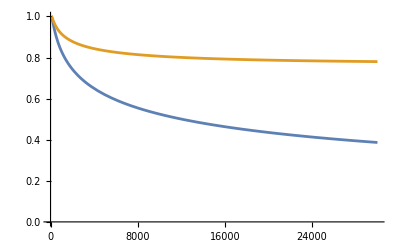

```mathematica
Plot[{σZhStandardModelExclusive[En]/σZhStandardModelTreeLevel[En],σZhStandardModelSemiInclusive[En]/σZhStandardModelTreeLevel[En]},{En,mw,30000},PlotRange->{0,1}]
```

Integrated cross-section at fixed energy (for example 10 TeV) as a function of the Wilson Coefficients

```mathematica
dibosonBSMPars={cW,cWtil,cHe[2,2],cHl1[2,2],cHl3[2,2]};
```

```mathematica
getσIntBSM[dσWWTreeLevel[0,0][10000^2,θ]][dibosonBSMPars][θmin,θmax]//FullSimplify
```

0.0038745+220.499 cW^2+220.499 cWtil^2+cHe[2,2] (-0.166907+125.787 cHe[2,2])+125.787 cHl1[2,2]^2+cHl1[2,2] (-0.328452-251.574 cHl3[2,2])+cHl3[2,2] (0.328452+125.787 cHl3[2,2])

The same function can be used for computing the cross-section in θ bins

```mathematica
θbins=Partition[Subdivide[θmin,θmax,10],2,1];
getσIntBSM[dσZhTreeLevel[0,0][10000^2,θ]][dibosonBSMPars]@@@θbins//FullSimplify//MatrixForm
```

(3.56433×10^-6+cHe[2,2] (-0.00554776+4.18099 cHe[2,2])+4.18099 cHl1[2,2]^2+cHl3[2,2] (0.00536955+4.18099 cHl3[2,2])+cHl1[2,2] (0.00536955+8.36198 cHl3[2,2])
7.11962×10^-6+cHe[2,2] (-0.0110814+8.35136 cHe[2,2])+8.35136 cHl1[2,2]^2+cHl3[2,2] (0.0107255+8.35136 cHl3[2,2])+cHl1[2,2] (0.0107255+16.7027 cHl3[2,2])
0.000011209+cHe[2,2] (-0.0174465+13.1483 cHe[2,2])+13.1483 cHl1[2,2]^2+cHl3[2,2] (0.0168861+13.1483 cHl3[2,2])+cHl1[2,2] (0.0168861+26.2966 cHl3[2,2])
0.0000148086+cHe[2,2] (-0.0230491+17.3706 cHe[2,2])+17.3706 cHl1[2,2]^2+cHl3[2,2] (0.0223087+17.3706 cHl3[2,2])+cHl1[2,2] (0.0223087+34.7412 cHl3[2,2])
0.0000169156+cHe[2,2] (-0.0263286+19.8421 cHe[2,2])+19.8421 cHl1[2,2]^2+cHl3[2,2] (0.0254828+19.8421 cHl3[2,2])+cHl1[2,2] (0.0254828+39.6843 cHl3[2,2])
0.0000169156+cHe[2,2] (-0.0263286+19.8421 cHe[2,2])+19.8421 cHl1[2,2]^2+cHl3[2,2] (0.0254828+19.8421 cHl3[2,2])+cHl1[2,2] (0.0254828+39.6843 cHl3[2,2])
0.0000148086+cHe[2,2] (-0.0230491+17.3706 cHe[2,2])+17.3706 cHl1[2,2]^2+cHl3[2,2] (0.0223087+17.3706 cHl3[2,2])+cHl1[2,2] (0.0223087+34.7412 cHl3[2,2])
0.000011209+cHe[2,2] (-0.0174465+13.1483 cHe[2,2])+13.1483 cHl1[2,2]^2+cHl3[2,2] (0.0168861+13.1483 cHl3[2,2])+cHl1[2,2] (0.0168861+26.2966 cHl3[2,2])
7.11962×10^-6+cHe[2,2] (-0.0110814+8.35136 cHe[2,2])+8.35136 cHl1[2,2]^2+cHl3[2,2] (0.0107255+8.35136 cHl3[2,2])+cHl1[2,2] (0.0107255+16.7027 cHl3[2,2])
3.56433×10^-6+cHe[2,2] (-0.00554776+4.18099 cHe[2,2])+4.18099 cHl1[2,2]^2+cHl3[2,2] (0.00536955+4.18099 cHl3[2,2])+cHl1[2,2] (0.00536955+8.36198 cHl3[2,2]))

### Expected Events

```mathematica
colliderS=10000^2;
```

Define 10 equally spaced θ bins and compute the expected number of events

```mathematica
θbins=Partition[Subdivide[θmin,θmax,10],2,1];
```

```mathematica
nExpZhTreeLevel=lum[colliderS]getσIntBSM[dσZhTreeLevel[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExpWWTreeLevel=lum[colliderS]getσIntBSM[dσWWTreeLevel[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
```

```mathematica
nExpZhExcl=lum[colliderS]getσIntBSM[dσZhExclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExpWWExcl=lum[colliderS]getσIntBSM[dσWWExclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
```

```mathematica
nExpZhSI=lum[colliderS]getσIntBSM[dσZhSemiInclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExpWWSI=lum[colliderS]getσIntBSM[dσWWSemiInclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExpWphSI=lum[colliderS]getσIntBSM[dσWphSemiInclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExphWmSI=lum[colliderS]getσIntBSM[dσhWmSemiInclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExpWpZSI=lum[colliderS]getσIntBSM[dσWpZSemiInclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
nExpZWmSI=lum[colliderS]getσIntBSM[dσZWmSemiInclusive[0,0][colliderS,θ]][dibosonBSMPars]@@@θbins;
```

The Zh and WW Semi-Inclusive cross-sections also include the Exclusive case. So we subtract it to get an independent “with radiation” process

```mathematica
nExpZhRad=nExpZhSI-nExpZhExcl;
nExpWWRad=nExpWWSI-nExpWWExcl;
```

## Difermion Production

### Born Amplitudes in the gauge basis

#### Born amplitudes

We compute the amplitudes for a single flavor combination. Differences in flavor can be added later. We only have to treat the muons as a special case. 
Because FormCalc does not work properly with four-fermion operators, we compute the amplitude by hand.

```mathematica
tt=-1/2 S(1-Cos[θ]);
uu=-1/2 S(1+Cos[θ]);
```

Leptons (excluding muons)

```mathematica
μRμRtoeReR={{lR2,lR2Bar,lR1,lR1Bar},Table[
-(gg1^2 yU1[lR2]yU1[lR1](1/S)+1/Λ^2(cee[1,1,2,2]+cee[1,2,2,1]+cee[2,1,1,2]+cee[2,2,1,1]))(2uu)
,{i,1,1},{j,1,1},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((gg1^2 Λ^2+S (cee[1,1,2,2]+cee[1,2,2,1]+cee[2,1,1,2]+cee[2,2,1,1])) (1+Cos[θ]))/Λ^2))

```mathematica
μLμLtoeReR={{L2,L2Bar,lR1,lR1Bar},Table[
(gg1^2 yU1[L2]yU1[lR1](1/S)+1/Λ^2 cle[2,2,1,1])(2tt)KroneckerDelta[i,j]
,{i,1,2},{j,1,2},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((gg1^2 Λ^2+2 S cle[2,2,1,1]) (-1+Cos[θ]))/(2 Λ^2)) | (0)
(0) | (((gg1^2 Λ^2+2 S cle[2,2,1,1]) (-1+Cos[θ]))/(2 Λ^2)))

```mathematica
μRμRtoeLeL={{lR2,lR2Bar,L1,L1Bar},Table[
(gg1^2 yU1[lR2]yU1[L1](1/S)+1/Λ^2 cle[1,1,2,2])(2tt)KroneckerDelta[k,l]
,{i,1,1},{j,1,1},{k,1,2},{l,1,2}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((gg1^2 Λ^2+2 S cle[1,1,2,2]) (-1+Cos[θ]))/(2 Λ^2) | 0
0 | ((gg1^2 Λ^2+2 S cle[1,1,2,2]) (-1+Cos[θ]))/(2 Λ^2)))

```mathematica
μLμLtoeLeL={{L2,L2Bar,L1,L1Bar},Table[
-(gg^2(1/S)+4 C3/Λ^2)(2uu)(1/2(KroneckerDelta[i,k]KroneckerDelta[j,l]-1/2 KroneckerDelta[i,j]KroneckerDelta[k,l]))
-(gg1^2 yU1[L2]yU1[L1](1/S)+C1/Λ^2)(2uu)KroneckerDelta[i,j]KroneckerDelta[k,l]
,{i,1,2},{j,1,2},{k,1,2},{l,1,2}]}/.{C1-> cll[1,1,2,2]+cll[2,2,1,1]+1/2(cll[1,2,2,1]+cll[2,1,1,2]),C3->1/2(cll[1,2,2,1]+cll[2,1,1,2])}//FullSimplify;
%[[2]]//MatrixForm
```

(((((gg^2+gg1^2) Λ^2+4 S (cll[1,1,2,2]+cll[1,2,2,1]+cll[2,1,1,2]+cll[2,2,1,1])) (1+Cos[θ]))/(4 Λ^2) | 0
0 | -(((gg-gg1) (gg+gg1) Λ^2-4 S (cll[1,1,2,2]+cll[2,2,1,1])) (1+Cos[θ]))/(4 Λ^2)) | (0 | ((gg^2 Λ^2+2 S (cll[1,2,2,1]+cll[2,1,1,2])) (1+Cos[θ]))/(2 Λ^2)
0 | 0)
(0 | 0
((gg^2 Λ^2+2 S (cll[1,2,2,1]+cll[2,1,1,2])) (1+Cos[θ]))/(2 Λ^2) | 0) | (-(((gg-gg1) (gg+gg1) Λ^2-4 S (cll[1,1,2,2]+cll[2,2,1,1])) (1+Cos[θ]))/(4 Λ^2) | 0
0 | (((gg^2+gg1^2) Λ^2+4 S (cll[1,1,2,2]+cll[1,2,2,1]+cll[2,1,1,2]+cll[2,2,1,1])) (1+Cos[θ]))/(4 Λ^2)))

Muons

```mathematica
μRμRtoμRμR={{lR2,lR2Bar,lR2,lR2Bar},Table[
-(gg1^2 yU1[lR2]yU1[lR2](1/S+1/tt)+4/Λ^2(cee[2,2,2,2]))(2uu)
,{i,1,1},{j,1,1},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((1+Cos[θ]) (4 S cee[2,2,2,2]-gg1^2 Λ^2 Cot[θ/2]^2))/Λ^2))

```mathematica
μLμLtoμRμR={{L2,L2Bar,lR2,lR2Bar},Table[
(gg1^2 yU1[lR2]yU1[L1](1/S)+1/Λ^2 cle[2,2,2,2])(2tt)KroneckerDelta[i,j]
,{i,1,2},{j,1,2},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((gg1^2 Λ^2+2 S cle[2,2,2,2]) (-1+Cos[θ]))/(2 Λ^2)) | (0)
(0) | (((gg1^2 Λ^2+2 S cle[2,2,2,2]) (-1+Cos[θ]))/(2 Λ^2)))

```mathematica
μRμRtoμLμL={{lR2,lR2Bar,L2,L2Bar},Table[
(gg1^2 yU1[lR2]yU1[L1](1/S)+1/Λ^2 cle[2,2,2,2])(2tt)KroneckerDelta[k,l]
,{i,1,1},{j,1,1},{k,1,2},{l,1,2}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((gg1^2 Λ^2+2 S cle[2,2,2,2]) (-1+Cos[θ]))/(2 Λ^2) | 0
0 | ((gg1^2 Λ^2+2 S cle[2,2,2,2]) (-1+Cos[θ]))/(2 Λ^2)))

```mathematica
μLμLtoμLμL={{L2,L2Bar,L2,L2Bar},Table[
-(gg^2(1/S)+4 C3/Λ^2)(2uu)(1/2(KroneckerDelta[i,k]KroneckerDelta[j,l]-1/2 KroneckerDelta[i,j]KroneckerDelta[k,l]))
-(gg^2(1/tt))(2uu)(1/2(KroneckerDelta[i,j]KroneckerDelta[k,l]-1/2 KroneckerDelta[i,k]KroneckerDelta[j,l]))
-(gg1^2 yU1[L2]yU1[L2](1/S)+C1/Λ^2)(2uu)KroneckerDelta[i,j]KroneckerDelta[k,l]
-(gg1^2 yU1[L2]yU1[L2](1/tt))(2uu)KroneckerDelta[i,k]KroneckerDelta[j,l]
,{i,1,2},{j,1,2},{k,1,2},{l,1,2}]}/.{C1-> 3cll[2,2,2,2],C3->cll[2,2,2,2]}//FullSimplify;
%[[2]]//MatrixForm
```

((-(((gg^2+gg1^2) Λ^2-16 S cll[2,2,2,2]+((gg^2+gg1^2) Λ^2+16 S cll[2,2,2,2]) Cos[θ]) Cot[θ/2]^2)/(4 Λ^2) | 0
0 | (((-5 gg^2+gg1^2) Λ^2+8 S cll[2,2,2,2]+((gg-gg1) (gg+gg1) Λ^2-8 S cll[2,2,2,2]) Cos[θ]) Cot[θ/2]^2)/(4 Λ^2)) | (0 | -(((-2 gg^2+gg1^2) Λ^2-4 S cll[2,2,2,2]+(gg^2 Λ^2+4 S cll[2,2,2,2]) Cos[θ]) Cot[θ/2]^2)/(2 Λ^2)
0 | 0)
(0 | 0
-(((-2 gg^2+gg1^2) Λ^2-4 S cll[2,2,2,2]+(gg^2 Λ^2+4 S cll[2,2,2,2]) Cos[θ]) Cot[θ/2]^2)/(2 Λ^2) | 0) | ((((-5 gg^2+gg1^2) Λ^2+8 S cll[2,2,2,2]+((gg-gg1) (gg+gg1) Λ^2-8 S cll[2,2,2,2]) Cos[θ]) Cot[θ/2]^2)/(4 Λ^2) | 0
0 | -(((gg^2+gg1^2) Λ^2-16 S cll[2,2,2,2]+((gg^2+gg1^2) Λ^2+16 S cll[2,2,2,2]) Cos[θ]) Cot[θ/2]^2)/(4 Λ^2)))

```mathematica
μRμLtoμRμL={{lR2,L2Bar,lR2,L2Bar},Table[
-(gg1^2 yU1[lR2]yU1[L2](1/tt)+cle[2,2,2,2]/Λ^2)(2S)KroneckerDelta[j,l]
,{i,1,1},{j,1,2},{k,1,1},{l,1,2}]}//FullSimplify;
%[[2]]//MatrixForm
```

((-(2 S cle[2,2,2,2])/Λ^2+gg1^2 Csc[θ/2]^2 | 0) | (0 | -(2 S cle[2,2,2,2])/Λ^2+gg1^2 Csc[θ/2]^2))

Quarks

```mathematica
μRμRtouRuR={{lR2,lR2Bar,uR1,uR1Bar},Table[
-(gg1^2 yU1[lR2]yU1[uR1](1/S)KroneckerDelta[flav1,flav2]+1/Λ^2(ceu[2,2,flav1,flav2]))(2uu)
,{i,1,1},{j,1,1},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((1/3 (1+Cos[θ]) ((3 S ceu[2,2,flav1,flav2])/Λ^2-2 gg1^2 flav1,flav2)))

```mathematica
μRμRtodRdR={{lR2,lR2Bar,dR1,dR1Bar},Table[
-(gg1^2 yU1[lR2]yU1[dR1](1/S)KroneckerDelta[flav1,flav2]+1/Λ^2(ced[2,2,flav1,flav2]))(2uu)
,{i,1,1},{j,1,1},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((1/3 (1+Cos[θ]) ((3 S ced[2,2,flav1,flav2])/Λ^2+gg1^2 flav1,flav2)))

```mathematica
μRμRtoQQ={{lR2,lR2Bar,Q1,Q1Bar},
Table[
(gg1^2 yU1[lR2]KroneckerDelta[flav1,flav2]yU1[Q1](1/S)+1/Λ^2 cqe[flav1,flav2,2,2])(2tt)KroneckerDelta[k,l]
,{i,1,1},{j,1,1},{k,1,2},{l,1,2}]}//FullSimplify;
%[[2]]//MatrixForm
```

((1/6 (-1+Cos[θ]) ((6 S cqe[flav1,flav2,2,2])/Λ^2-gg1^2 flav1,flav2) | 0
0 | 1/6 (-1+Cos[θ]) ((6 S cqe[flav1,flav2,2,2])/Λ^2-gg1^2 flav1,flav2)))

```mathematica
μLμLtouRuR={{L2,L2Bar,uR1,uR1Bar},Table[
(gg1^2 yU1[L2]yU1[uR1](1/S)KroneckerDelta[flav1,flav2]+1/Λ^2 clu[2,2,flav1,flav2])(2tt)KroneckerDelta[i,j]
,{i,1,2},{j,1,2},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((1/3 (-1+Cos[θ]) ((3 S clu[2,2,flav1,flav2])/Λ^2-gg1^2 flav1,flav2)) | (0)
(0) | (1/3 (-1+Cos[θ]) ((3 S clu[2,2,flav1,flav2])/Λ^2-gg1^2 flav1,flav2)))

```mathematica
μLμLtodRdR={{L2,L2Bar,dR1,dR1Bar},Table[
(gg1^2 yU1[L2]yU1[dR1](1/S)KroneckerDelta[flav1,flav2]+1/Λ^2 cld[2,2,flav1,flav2])(2tt)KroneckerDelta[i,j]
,{i,1,2},{j,1,2},{k,1,1},{l,1,1}]}//FullSimplify;
%[[2]]//MatrixForm
```

((((-1+Cos[θ]) (6 S cld[2,2,flav1,flav2]+gg1^2 Λ^2 flav1,flav2))/(6 Λ^2)) | (0)
(0) | (((-1+Cos[θ]) (6 S cld[2,2,flav1,flav2]+gg1^2 Λ^2 flav1,flav2))/(6 Λ^2)))

```mathematica
μLμLtoQQ={{L2,L2Bar,Q1,Q1Bar},
Table[
-(gg^2(1/S)KroneckerDelta[flav1,flav2]+4 clq3[2,2,flav1,flav2]/Λ^2)(2uu)(1/2(KroneckerDelta[i,k]KroneckerDelta[j,l]-1/2 KroneckerDelta[i,j]KroneckerDelta[k,l]))
-(gg1^2 yU1[L2]yU1[Q1](1/S)KroneckerDelta[flav1,flav2]+clq1[2,2,flav1,flav2]/Λ^2)(2uu)KroneckerDelta[i,j]KroneckerDelta[k,l]
,{i,1,2},{j,1,2},{k,1,2},{l,1,2}]
}//FullSimplify;
%[[2]]//MatrixForm
```

((1/12 (1+Cos[θ]) ((12 S (clq1[2,2,flav1,flav2]+clq3[2,2,flav1,flav2]))/Λ^2+(3 gg^2-gg1^2) flav1,flav2) | 0
0 | (S (clq1[2,2,flav1,flav2]-clq3[2,2,flav1,flav2]) (1+Cos[θ]))/Λ^2-1/12 (3 gg^2+gg1^2) (1+Cos[θ]) flav1,flav2) | (0 | ((1+Cos[θ]) (4 S clq3[2,2,flav1,flav2]+gg^2 Λ^2 flav1,flav2))/(2 Λ^2)
0 | 0)
(0 | 0
((1+Cos[θ]) (4 S clq3[2,2,flav1,flav2]+gg^2 Λ^2 flav1,flav2))/(2 Λ^2) | 0) | ((S (clq1[2,2,flav1,flav2]-clq3[2,2,flav1,flav2]) (1+Cos[θ]))/Λ^2-1/12 (3 gg^2+gg1^2) (1+Cos[θ]) flav1,flav2 | 0
0 | 1/12 (1+Cos[θ]) ((12 S (clq1[2,2,flav1,flav2]+clq3[2,2,flav1,flav2]))/Λ^2+(3 gg^2-gg1^2) flav1,flav2)))

#### Adding RG Evolution

```mathematica
μRμRtoeReRRG=ReplacePart[μRμRtoeReR,2->μRμRtoeReR[[2]]/.toRG[S]];
μRμRtoeLeLRG=ReplacePart[μRμRtoeLeL,2->μRμRtoeLeL[[2]]/.toRG[S]];
μLμLtoeReRRG=ReplacePart[μLμLtoeReR,2->μLμLtoeReR[[2]]/.toRG[S]];
μLμLtoeLeLRG=ReplacePart[μLμLtoeLeL,2->μLμLtoeLeL[[2]]/.toRG[S]];

μRμRtoμRμRRG=ReplacePart[μRμRtoμRμR,2->μRμRtoμRμR[[2]]/.toRG[S]];
μRμRtoμLμLRG=ReplacePart[μRμRtoμLμL,2->μRμRtoμLμL[[2]]/.toRG[S]];
μLμLtoμRμRRG=ReplacePart[μLμLtoμRμR,2->μLμLtoμRμR[[2]]/.toRG[S]];
μLμLtoμLμLRG=ReplacePart[μLμLtoμLμL,2->μLμLtoμLμL[[2]]/.toRG[S]];
μRμLtoμRμLRG=ReplacePart[μRμLtoμRμL,2->μRμLtoμRμL[[2]]/.toRG[S]];

μRμRtouRuRRG=ReplacePart[μRμRtouRuR,2->μRμRtouRuR[[2]]/.toRG[S]];
μRμRtodRdRRG=ReplacePart[μRμRtodRdR,2->μRμRtodRdR[[2]]/.toRG[S]];
μRμRtoQQRG=ReplacePart[μRμRtoQQ,2->μRμRtoQQ[[2]]/.toRG[S]];
μLμLtouRuRRG=ReplacePart[μLμLtouRuR,2->μLμLtouRuR[[2]]/.toRG[S]];
μLμLtodRdRRG=ReplacePart[μLμLtodRdR,2->μLμLtodRdR[[2]]/.toRG[S]];
μLμLtoQQRG=ReplacePart[μLμLtoQQ,2->μLμLtoQQ[[2]]/.toRG[S]];
```

### Density matrices

#### Born Level

```mathematica
μRμRtoeReRBornDM=computeBornDM[μRμRtoeReRRG];
μRμRtoeLeLBornDM=computeBornDM[μRμRtoeLeLRG];
μLμLtoeReRBornDM=computeBornDM[μLμLtoeReRRG];
μLμLtoeLeLBornDM=computeBornDM[μLμLtoeLeLRG];

μRμRtoμRμRBornDM=computeBornDM[μRμRtoμRμRRG];
μRμRtoμLμLBornDM=computeBornDM[μRμRtoμLμLRG];
μLμLtoμRμRBornDM=computeBornDM[μLμLtoμRμRRG];
μLμLtoμLμLBornDM=computeBornDM[μLμLtoμLμLRG];
μRμLtoμRμLBornDM=computeBornDM[μRμLtoμRμLRG];

μRμRtouRuRBornDM=computeBornDM[μRμRtouRuRRG];
μRμRtodRdRBornDM=computeBornDM[μRμRtodRdRRG];
μRμRtoQQBornDM=computeBornDM[μRμRtoQQRG];
μLμLtouRuRBornDM=computeBornDM[μLμLtouRuRRG];
μLμLtodRdRBornDM=computeBornDM[μLμLtodRdRRG];
μLμLtoQQBornDM=computeBornDM[μLμLtoQQRG];
```

#### Exclusive DL

```mathematica
μRμRtoeReRExclusiveDM=computeExclusiveDM[μRμRtoeReRRG];
μRμRtoeLeLExclusiveDM=computeExclusiveDM[μRμRtoeLeLRG];
μLμLtoeReRExclusiveDM=computeExclusiveDM[μLμLtoeReRRG];
μLμLtoeLeLExclusiveDM=computeExclusiveDM[μLμLtoeLeLRG];

μRμRtoμRμRExclusiveDM=computeExclusiveDM[μRμRtoμRμRRG];
μRμRtoμLμLExclusiveDM=computeExclusiveDM[μRμRtoμLμLRG];
μLμLtoμRμRExclusiveDM=computeExclusiveDM[μLμLtoμRμRRG];
μLμLtoμLμLExclusiveDM=computeExclusiveDM[μLμLtoμLμLRG];
μRμLtoμRμLExclusiveDM=computeExclusiveDM[μRμLtoμRμLRG];

μRμRtouRuRExclusiveDM=computeExclusiveDM[μRμRtouRuRRG];
μRμRtodRdRExclusiveDM=computeExclusiveDM[μRμRtodRdRRG];
μRμRtoQQExclusiveDM=computeExclusiveDM[μRμRtoQQRG];
μLμLtouRuRExclusiveDM=computeExclusiveDM[μLμLtouRuRRG];
μLμLtodRdRExclusiveDM=computeExclusiveDM[μLμLtodRdRRG];
μLμLtoQQExclusiveDM=computeExclusiveDM[μLμLtoQQRG];
```

#### Semi-inclusive DL

```mathematica
μRμRtoeReRSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoeReRRG];
μRμRtoeLeLSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoeLeLRG];
μLμLtoeReRSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoeReRRG];
μLμLtoeLeLSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoeLeLRG];

μRμRtoμRμRSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoμRμRRG];
μRμRtoμLμLSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoμLμLRG];
μLμLtoμRμRSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoμRμRRG];
μLμLtoμLμLSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoμLμLRG];
μRμLtoμRμLSemiInclusiveDM=computeSemiInclusiveDM[μRμLtoμRμLRG];

μRμRtouRuRSemiInclusiveDM=computeSemiInclusiveDM[μRμRtouRuRRG];
μRμRtodRdRSemiInclusiveDM=computeSemiInclusiveDM[μRμRtodRdRRG];
μRμRtoQQSemiInclusiveDM=computeSemiInclusiveDM[μRμRtoQQRG];
μLμLtouRuRSemiInclusiveDM=computeSemiInclusiveDM[μLμLtouRuRRG];
μLμLtodRdRSemiInclusiveDM=computeSemiInclusiveDM[μLμLtodRdRRG];
μLμLtoQQSemiInclusiveDM=computeSemiInclusiveDM[μLμLtoQQRG];
```

### Computing (polarized) squared matrix elements

#### Leptons (no muon)

```mathematica
RRtoeReRAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_R","(e^+)_R",μRμRtoeReRBornDM];
RRtoeLeLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_L","(e^+)_L",μRμRtoeLeLBornDM];
LLtoeReRAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_R","(e^+)_R",μLμLtoeReRBornDM];
LLtoeLeLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_L","(e^+)_L",μLμLtoeLeLBornDM];
```

```mathematica
RRtoeReRAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_R","(e^+)_R",μRμRtoeReRExclusiveDM];
RRtoeLeLAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_L","(e^+)_L",μRμRtoeLeLExclusiveDM];
LLtoeReRAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_R","(e^+)_R",μLμLtoeReRExclusiveDM];
LLtoeLeLAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_L","(e^+)_L",μLμLtoeLeLExclusiveDM];
```

```mathematica
RRtoeReRAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_R","(e^+)_R",μRμRtoeReRSemiInclusiveDM];
RRtoeLeLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_L","(e^+)_L",μRμRtoeLeLSemiInclusiveDM];
LLtoeReRAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_R","(e^+)_R",μLμLtoeReRSemiInclusiveDM];
LLtoeLeLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_L","(e^+)_L",μLμLtoeLeLSemiInclusiveDM];
```

```mathematica
RRtoeReRAmpSqTreeLevel
```

((1+Cos[θ])^2 (S (cee[1,1,2,2]+cee[1,2,2,1]+cee[2,1,1,2]+cee[2,2,1,1])+(40 gg1^2 π^2 Λ^2)/(40 π^2+11 gg1^2 Log[MZ2]-11 gg1^2 Log[S]))^2)/Λ^4

#### Muons

```mathematica
RRtoμRμRAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_R","(μ^+)_R",μRμRtoμRμRBornDM];
RRtoμLμLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_L","(μ^+)_L",μRμRtoμLμLBornDM];
LLtoμRμRAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_R","(μ^+)_R",μLμLtoμRμRBornDM];
LLtoμLμLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_L","(μ^+)_L",μLμLtoμLμLBornDM];
RLtoμRμLAmpSqTreeLevel=getSquaredAmplitude["(μ^-)_R","(μ^+)_L","(μ^-)_R","(μ^+)_L",μRμLtoμRμLBornDM];
LRtoμLμRAmpSqTreeLevel=RLtoμRμLAmpSqTreeLevel;
```

```mathematica
RRtoμRμRAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_R","(μ^+)_R",μRμRtoμRμRExclusiveDM];
RRtoμLμLAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_L","(μ^+)_L",μRμRtoμLμLExclusiveDM];
LLtoμRμRAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_R","(μ^+)_R",μLμLtoμRμRExclusiveDM];
LLtoμLμLAmpSqExclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_L","(μ^+)_L",μLμLtoμLμLExclusiveDM];
RLtoμRμLAmpSqExclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_L","(μ^-)_R","(μ^+)_L",μRμLtoμRμLExclusiveDM];
LRtoμLμRAmpSqExclusive=RLtoμRμLAmpSqExclusive;
```

```mathematica
RRtoμRμRAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_R","(μ^+)_R",μRμRtoμRμRSemiInclusiveDM];
RRtoμLμLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_L","(μ^+)_L",μRμRtoμLμLSemiInclusiveDM];
LLtoμRμRAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_R","(μ^+)_R",μLμLtoμRμRSemiInclusiveDM];
LLtoμLμLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_L","(μ^+)_L",μLμLtoμLμLSemiInclusiveDM];
RLtoμRμLAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_L","(μ^-)_R","(μ^+)_L",μRμLtoμRμLSemiInclusiveDM];
LRtoμLμRAmpSqSemiInclusive=RLtoμRμLAmpSqSemiInclusive;
```

#### Quarks

```mathematica
RRtouRuRAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_R","(ū)_R",μRμRtouRuRBornDM];
RRtouLuLAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_L","(ū)_L",μRμRtoQQBornDM];
LLtouRuRAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_R","(ū)_R",μLμLtouRuRBornDM];
LLtouLuLAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_L","(ū)_L",μLμLtoQQBornDM];
RRtodRdRAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_R","(d̄)_R",μRμRtodRdRBornDM];
RRtodLdLAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_L","(d̄)_L",μRμRtoQQBornDM];
LLtodRdRAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_R","(d̄)_R",μLμLtodRdRBornDM];
LLtodLdLAmpSqTreeLevel=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_L","(d̄)_L",μLμLtoQQBornDM];
```

```mathematica
RRtouRuRAmpSqExclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_R","(ū)_R",μRμRtouRuRExclusiveDM];
RRtouLuLAmpSqExclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_L","(ū)_L",μRμRtoQQExclusiveDM];
LLtouRuRAmpSqExclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_R","(ū)_R",μLμLtouRuRExclusiveDM];
LLtouLuLAmpSqExclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_L","(ū)_L",μLμLtoQQExclusiveDM];
RRtodRdRAmpSqExclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_R","(d̄)_R",μRμRtodRdRExclusiveDM];
RRtodLdLAmpSqExclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_L","(d̄)_L",μRμRtoQQExclusiveDM];
LLtodRdRAmpSqExclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_R","(d̄)_R",μLμLtodRdRExclusiveDM];
LLtodLdLAmpSqExclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_L","(d̄)_L",μLμLtoQQExclusiveDM];
```

```mathematica
RRtouRuRAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_R","(ū)_R",μRμRtouRuRSemiInclusiveDM];
RRtouLuLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_L","(ū)_L",μRμRtoQQSemiInclusiveDM];
LLtouRuRAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_R","(ū)_R",μLμLtouRuRSemiInclusiveDM];
LLtouLuLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_L","(ū)_L",μLμLtoQQSemiInclusiveDM];
RRtodRdRAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_R","(d̄)_R",μRμRtodRdRSemiInclusiveDM];
RRtodLdLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_L","(d̄)_L",μRμRtoQQSemiInclusiveDM];
LLtodRdRAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_R","(d̄)_R",μLμLtodRdRSemiInclusiveDM];
LLtodLdLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_L","(d̄)_L",μLμLtoQQSemiInclusiveDM];
```

#### Charged Lepton

```mathematica
RRtoLmνAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(e^-)_L","(ν̄)_e",μRμRtoeLeLSemiInclusiveDM];
LLtoLmνAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(e^-)_L","(ν̄)_e",μLμLtoeLeLSemiInclusiveDM];
RRtoνLpAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","ν_e","(e^+)_L",μRμRtoeLeLSemiInclusiveDM];
LLtoνLpAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","ν_e","(e^+)_L",μLμLtoeLeLSemiInclusiveDM];
```

#### Charged muon

```mathematica
RRtoμLmνAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","(μ^-)_L","(ν̄)_μ",μRμRtoμLμLSemiInclusiveDM];
LLtoμLmνAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","(μ^-)_L","(ν̄)_μ",μLμLtoμLμLSemiInclusiveDM];
RRtoνμLpAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_R","ν_μ","(μ^+)_L",μRμRtoμLμLSemiInclusiveDM];
LLtoνμLpAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_L","(μ^+)_L","ν_μ","(μ^+)_L",μLμLtoμLμLSemiInclusiveDM];
```

```mathematica
RLtoμRmνAmpSqSemiInclusive=getSquaredAmplitude["(μ^-)_R","(μ^+)_L","(μ^-)_R","(ν̄)_μ",μRμLtoμRμLSemiInclusiveDM];
LRtoνμRpAmpSqSemiInclusive=RLtoμRmνAmpSqSemiInclusive;
```

#### Charged Quark

```mathematica
RRtouLdLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","u_L","(d̄)_L",μRμRtoQQSemiInclusiveDM];
LLtouLdLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","u_L","(d̄)_L",μLμLtoQQSemiInclusiveDM];
RRtodLuLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_R","(μ^+)_R","d_L","(ū)_L",μRμRtoQQSemiInclusiveDM];
LLtodLuLAmpSqSemiInclusive=3getSquaredAmplitude["(μ^-)_L","(μ^+)_L","d_L","(ū)_L",μLμLtoQQSemiInclusiveDM];
```

### Differential Cross Sections

```mathematica
dσeeTreeLevel[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoeLeLAmpSqTreeLevel+LLtoeReRAmpSqTreeLevel,RRtoeLeLAmpSqTreeLevel+RRtoeReRAmpSqTreeLevel]//.toNumbers;
dσeeExclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoeLeLAmpSqExclusive+LLtoeReRAmpSqExclusive,RRtoeLeLAmpSqExclusive+RRtoeReRAmpSqExclusive]//.toNumbers;
dσeeSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoeLeLAmpSqSemiInclusive+LLtoeReRAmpSqSemiInclusive,RRtoeLeLAmpSqSemiInclusive+RRtoeReRAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσμμTreeLevel[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoμLμLAmpSqTreeLevel+LLtoμRμRAmpSqTreeLevel,RRtoμLμLAmpSqTreeLevel+RRtoμRμRAmpSqTreeLevel,RLtoμRμLAmpSqTreeLevel,LRtoμLμRAmpSqTreeLevel]//.toNumbers;
dσμμExclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoμLμLAmpSqExclusive+LLtoμRμRAmpSqExclusive,RRtoμLμLAmpSqExclusive+RRtoμRμRAmpSqExclusive,RLtoμRμLAmpSqExclusive,LRtoμLμRAmpSqExclusive]//.toNumbers;
dσμμSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoμLμLAmpSqSemiInclusive+LLtoμRμRAmpSqSemiInclusive,RRtoμLμLAmpSqSemiInclusive+RRtoμRμRAmpSqSemiInclusive,RLtoμRμLAmpSqSemiInclusive,LRtoμLμRAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσemνSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoLmνAmpSqSemiInclusive,RRtoLmνAmpSqSemiInclusive]//.toNumbers;
dσνepSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoνLpAmpSqSemiInclusive,RRtoνLpAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσμmνSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoμLmνAmpSqSemiInclusive,RRtoμLmνAmpSqSemiInclusive,RLtoμRmνAmpSqSemiInclusive,0]//.toNumbers;
dσνμpSemiInclusive[polm_,polp_][S_,θ_]=poldσ[polm,polp][LLtoνμLpAmpSqSemiInclusive,RRtoνμLpAmpSqSemiInclusive,0,LRtoνμRpAmpSqSemiInclusive]//.toNumbers;
```

```mathematica
dσuuTreeLevel[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtouLuLAmpSqTreeLevel+LLtouRuRAmpSqTreeLevel,RRtouLuLAmpSqTreeLevel+RRtouRuRAmpSqTreeLevel],{f1,1,3},{f2,1,3}]//.toNumbers;
dσuuExclusive[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtouLuLAmpSqExclusive+LLtouRuRAmpSqExclusive,RRtouLuLAmpSqExclusive+RRtouRuRAmpSqExclusive],{f1,1,3},{f2,1,3}]//.toNumbers;
dσuuSemiInclusive[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtouLuLAmpSqSemiInclusive+LLtouRuRAmpSqSemiInclusive,RRtouLuLAmpSqSemiInclusive+RRtouRuRAmpSqSemiInclusive],{f1,1,3},{f2,1,3}]//.toNumbers;
```

```mathematica
dσddTreeLevel[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtodLdLAmpSqTreeLevel+LLtodRdRAmpSqTreeLevel,RRtodLdLAmpSqTreeLevel+RRtodRdRAmpSqTreeLevel],{f1,1,3},{f2,1,3}]//.toNumbers;
dσddExclusive[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtodLdLAmpSqExclusive+LLtodRdRAmpSqExclusive,RRtodLdLAmpSqExclusive+RRtodRdRAmpSqExclusive],{f1,1,3},{f2,1,3}]//.toNumbers;
dσddSemiInclusive[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtodLdLAmpSqSemiInclusive+LLtodRdRAmpSqSemiInclusive,RRtodLdLAmpSqSemiInclusive+RRtodRdRAmpSqSemiInclusive],{f1,1,3},{f2,1,3}]//.toNumbers;
```

```mathematica
dσudSemiInclusive[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtouLdLAmpSqSemiInclusive,RRtouLdLAmpSqSemiInclusive],{f1,1,3},{f2,1,3}]//.toNumbers;
dσduSemiInclusive[polm_,polp_][S_,θ_]=Table[poldσ[polm,polp][LLtodLuLAmpSqSemiInclusive,RRtodLuLAmpSqSemiInclusive],{f1,1,3},{f2,1,3}]//.toNumbers;
```

### Expected Events

```mathematica
colliderS=10000^2;
```

```mathematica
difermionBSMPars={cee[__],cll[__],cle[__],ceu[__],ced[__],clq1[__],clq3[__],cqe[__],clu[__],cld[__]};
difermionBSMParsHeads={cee,cll,cle,ceu,ced,clq1,clq3,cqe,clu,cld};
dileptonBSMPars={cee,cll,cll1,cle};
diquarkBSMpars={ceu,ced,clq1,clq3,clu,cld,cqe};
```

```mathematica
θbins=Partition[Subdivide[θmin,θmax,10],2,1];
```

```mathematica
flavorReplace[i_->j_]:=(f_Symbol/;MemberQ[difermionBSMParsHeads,f])[args___]:>f@@Replace[{args},i->j,{1}]
```

```mathematica
flavorUniversal:={
cee[i_,j_,k_,l_]:>1/2 cee (KroneckerDelta[i,j]KroneckerDelta[k,l]+KroneckerDelta[i,l]KroneckerDelta[j,k]),
cll[i_,j_,k_,l_]:>cll (KroneckerDelta[i,j]KroneckerDelta[k,l])+cll1(KroneckerDelta[i,l]KroneckerDelta[j,k]),
cle[i_,j_,k_,l_]:>cle KroneckerDelta[i,j]KroneckerDelta[k,l],
ceu[i_,j_,k_,l_]:>ceu KroneckerDelta[i,j]KroneckerDelta[k,l],
ced[i_,j_,k_,l_]:>ced KroneckerDelta[i,j]KroneckerDelta[k,l],
clq1[i_,j_,k_,l_]:>clq1 KroneckerDelta[i,j]KroneckerDelta[k,l],
clq3[i_,j_,k_,l_]:>clq3 KroneckerDelta[i,j]KroneckerDelta[k,l],
cqe[i_,j_,k_,l_]:>cqe KroneckerDelta[i,j]KroneckerDelta[k,l],
clu[i_,j_,k_,l_]:>clu KroneckerDelta[i,j]KroneckerDelta[k,l],
cld[i_,j_,k_,l_]:>cld KroneckerDelta[i,j]KroneckerDelta[k,l]
}
```

Dilepton

```mathematica
nExpeeTreeLevel=lum[colliderS]getσIntBSM[dσeeTreeLevel[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpμμTreeLevel=lum[colliderS]getσIntBSM[dσμμTreeLevel[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpττTreeLevel=lum[colliderS]getσIntBSM[dσeeTreeLevel[0,0][colliderS,θ]][difermionBSMPars]@@@θbins/.flavorReplace[1->3];
```

```mathematica
nExpeeExcl=lum[colliderS]getσIntBSM[dσeeExclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpμμExcl=lum[colliderS]getσIntBSM[dσμμExclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpττExcl=lum[colliderS]getσIntBSM[dσeeExclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins/.flavorReplace[1->3];
```

```mathematica
nExpeeSI=lum[colliderS]getσIntBSM[dσeeSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpμμSI=lum[colliderS]getσIntBSM[dσμμSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpττSI=lum[colliderS]getσIntBSM[dσeeSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins/.flavorReplace[1->3];
```

```mathematica
nExpemνSI=lum[colliderS]getσIntBSM[dσemνSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpμmνSI=lum[colliderS]getσIntBSM[dσμmνSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpτmνSI=lum[colliderS]getσIntBSM[dσemνSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins/.flavorReplace[1->3];
nExpνepSI=lum[colliderS]getσIntBSM[dσνepSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpνμpSI=lum[colliderS]getσIntBSM[dσνμpSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins;
nExpντpSI=lum[colliderS]getσIntBSM[dσνepSemiInclusive[0,0][colliderS,θ]][difermionBSMPars]@@@θbins/.flavorReplace[1->3];
```

```mathematica
nExpeeRad=nExpeeSI-nExpeeExcl;
nExpμμRad=nExpμμSI-nExpμμExcl;
nExpττRad=nExpττSI-nExpττExcl;
```

Diquark

```mathematica
nExpuuTreeLevel=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσuuTreeLevel[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
nExpddTreeLevel=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσddTreeLevel[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
```

```mathematica
nExpuuExcl=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσuuExclusive[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
nExpddExcl=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσddExclusive[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
```

```mathematica
nExpuuSI=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσuuSemiInclusive[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
nExpddSI=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσddSemiInclusive[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
nExpudSI=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσudSemiInclusive[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
nExpduSI=lum[colliderS]ParallelMap[getσIntBSM[#][difermionBSMPars]@@@θbins&,Flatten@dσduSemiInclusive[0,0][colliderS,θ]]//ArrayReshape[#,{3,3,Length[θbins]}]&;
```

```mathematica
nExpuuRad=nExpuuSI-nExpuuExcl;
nExpddRad=nExpddSI-nExpddExcl;
```

## Exporting Results

```mathematica
outputFolder=NotebookDirectory[]<>"/Results10TeV";
```

```mathematica
DumpSave[outputFolder<>"/Diboson/DibosonTreeLevel.mx",{nExpZhTreeLevel,nExpWWTreeLevel}];
DumpSave[outputFolder<>"/Diboson/DibosonExclusive.mx",{nExpZhExcl,nExpWWExcl}];
DumpSave[outputFolder<>"/Diboson/DibosonWithRadiation.mx",{nExpZhRad,nExpWWRad,nExpWpZSI,nExpZWmSI,nExpWphSI,nExphWmSI}];
```

```mathematica
DumpSave[outputFolder<>"/Difermion/DileptonTreeLevel.mx",{nExpeeTreeLevel,nExpμμTreeLevel,nExpττTreeLevel}];
DumpSave[outputFolder<>"/Difermion/DileptonExclusive.mx",{nExpeeExcl,nExpμμExcl,nExpττExcl}];
DumpSave[outputFolder<>"/Difermion/DileptonWithRadiation.mx",{nExpeeRad,nExpμμRad,nExpττRad,nExpemνSI,nExpμmνSI,nExpτmνSI,nExpνepSI,nExpνμpSI,nExpντpSI}];
```

```mathematica
DumpSave[outputFolder<>"/Difermion/DiquarkTreeLevel.mx",{nExpuuTreeLevel,nExpddTreeLevel}];
DumpSave[outputFolder<>"/Difermion/DiquarkExclusive.mx",{nExpuuExcl,nExpddExcl}];
DumpSave[outputFolder<>"/Difermion/DiquarkWithRadiation.mx",{nExpuuRad,nExpddRad,nExpudSI,nExpduSI}];
```